# Summer-End Report

Tom Eichlersmith
August 2016

## Introduction

We started the summer with the end goal of understanding how the shape of the border of a drum affects the resonant frequencies produced, so that we could make the ‘best’ sounding drum shape (‘best’ being defined as sounds closest to perfectly tonal). This project quickly expanded into many different and exciting branches which required study. In this report, I will focus heavily on the Computational Optimization part of this project, since that is the part I spent my time working on and therefore understand the most.

## Computational Optimization

Our first (perhaps erroneous) assumption was that the membrane was the most important contributor to the sounds produced when a drum is struck and thus that all other parts, such as the frame and air around the membrane, could be ignored. This simplified our calculations to determining the eigensystem of the two dimensional laplacian in a certain region. It would be interesting to investigate these changes in the border shape with the other parts considered, but we did not do so in this project.
Very quickly, we realized that the work divided into two sections: (1) Calculating the eigensystem for a certain region and (2) Rating the eigenfrequencies on an objective scale to determine a measure of how ‘good’ the shape sounds.
When (1) and (2) are satisfactorily completed, we can begin running different optimization schemes in order to find the ‘best’ sounding border.

### (1) Eigensystem Calculation

We wanted to represent an individual border as a two dimensional parametrization in order to give us as much flexibilty as possible, so now, a ‘border’ shall be defined as a simple closed curve parametrization represented as the list {{x[u],y[u]},{u_min,u_max}}.

Mathematica 10.2+ has the function NDEigensystem[...] that is able to do the calculations that we need. In actuality, since our differential equation remains the same, we can construct our own function to determine the eigensystem for a particular region:

```mathematica
egsystem::usage="egsystem[Num,const][region] determines the eigensystem up to Num'th eigenvalue for the given region
-const is multiplied into Laplacian and is optional, default = 1";
egsystem[Num_?(IntegerQ[#]&&Positive[#]&),const_:1][region_?RegionQ]:=Module[{f,freqs,vals,funcs}, {vals,funcs}=NDEigensystem[{-const Laplacian[f[x,y],{x,y}],DirichletCondition[f[x,y]==0,True]},{f},{x,y}∈region,Num];
freqs=√vals;
{freqs,funcs}];
```

But now we must determine the region enclosed by a border so we can continually represent different shapes by their borders. Through some Mathematica trial and error, we ended with a BoundaryMeshRegion using points extracted from ParametricPlot:

```mathematica
parametricregion::usage="parametricregion[{{f,g},{umin,umax}}] produces a region from the input simple closed parametrized border
-f,g are the *heads* of the border functions";
parametricregion[{{f_,g_},{umin_,umax_}}]:=Module[{pts,plot},
plot=ParametricPlot[{f[u],g[u]},{u,umin,umax}];
pts=Flatten[Table[plot[[1,1,3,i,1]],{i,2,Length[Position[plot,Line]]+1}],1];
pts=DeleteDuplicates[pts];
BoundaryMeshRegion[pts,Line[Join[Range[Length[pts]-1],{1}]]]];
```

With these two (relatively simple and concise) functions, we are able to determine the eigensystem for any simple closed curve acting as a border.

```mathematica
Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Weird Test Shape/WeirdTest EShapes.jpg"]
```

-Graphics-

### (2) Rating Eigenfrequencies

String and wind instruments have eigenfrequencies that are perfectly harmonic, that is, every frequency is a multiple of the fundamental (lowest) frequency. If we consider these instruments to be perfect in the sense of how we have defined ‘good’ sound, we can treat the set Π={f,2f,3f,4f,5f,...} as the set of perfect eigenfrequencies. This naturally leads to some simple, mathematical, measurements of how good a general set of frequencies Ω={a,b,c,d,...} (a>b>c>d>...) sounds.

#### Variance of Differences

Define Ω^*={b-a,c-b,d-c,...}. If Ω is perfectly harmonic, then the variance of Ω^* would be zero. Therefore, we can define v=Var(Ω^*) and say that v is a measure of the perfection of the frequencies Ω and as v→0, the frequencies approach perfection.
Allowing for some frequencies to be so close they sound the same (d_min), we define the function:

```mathematica
vard::usage="vard[dmin][Ω] outputs the variance in the differences of the input list of frequencies Ω
-dmin is optional, default = 0.1";
vard[dmin_:0.1][Ω_List]:=Module[{Ωstar,i},
Ωstar={Ω[[2]]-Ω[[1]]};
For[i=2,i<Length[Ω],i++,AppendTo[Ωstar,Ω[[i+1]]-Ω[[i]]]];
For[i=1,i≤Length[Ωstar],i++,If[Ωstar[[i]]≤dmin,Ωstar=Delete[Ωstar,i]]];
Variance[Ωstar]];
```

#### “Displacement” Vector

If we wish to be slightly more complicated to attain more information, we can determine the set Π which is closest to Ω (the integer values of the linear fit of Ω) and then find how far off each member of Ω is from its corresponding member in Π. These differences can represent the “displacement” of Ω from Π.
Allowing for some frequencies to be so close they sound the same (r_min), we define the function:

```mathematica
disvector::usage="disvector[rmin][Ω] outputs a 'displacement' vector where each element is the distance a frequency is from a corresponding perfect frequency
-rmin is optional, default = 1.01";
disvector[rmin_:1.01][Ω_List]:=Module[{freqs,number,line,perf,displacement,i},
freqs={{1,Ω[[1]]}};
number=1;
For[i=2,i≤Length[Ω],i++,
If[Ω[[i]]/Ω[[i-1]]≤rmin,AppendTo[freqs,{number,Ω[[i]]}],AppendTo[freqs,{++number,Ω[[i]]}]]
];
line[t_]:=(Fit[freqs,{t},t]//Evaluate);
perf=Map[line,freqs[[All,1]]];
displacement=freqs[[All,2]]-perf;
displacement];
```

Both of the above approaches are a completely mathematical approach to rating a list of frequencies. The next approach allows for more flexibility in the rating system, but is less transparent.

#### Neural Network

Mathematica has a command (Predict[..., Method->”NeuralNetwork”]), which builds a Neural Network from a given trainging set. We decided our data would be represented by the five lowest frequencies, normalized so that the fundamental would always equal one, and rated on a scale of one to five.
The most difficult part about using a Neural Network is developing a training set that will teach the Neural Network to do what you wish it to do. Given not much time or participants, we decided to develop a relatively smaller training set by listening to randomly generated sets of frequencies and rating them and then appending known sets of frequencies rated perfect.

### Complications

#### Intensity

As seen above, different eigenfrequencies have different corresponding shapes of their representative eigenfunction. Depending on where a membrane is hit, different eigenfuncitons (and therefore different frequencies) are excited at varying intensities. Sometimes a specific frequency becomes in-audible because of where it was hit; therefore, we were forced to also model the hitting of a drum, so that we can point out which frequencies might not be seen in the analysis of an actual sound.
One (more precise) solution to this problem is to include the time-domain in the solution to the differential equation instead of simplifying it out. We were able to gather some useful qualitative data from this procedure; however, it was much too slow (about 10 to 15 minutes per calculation) for our purposes.
The next best solution is to define a function that models the shape of the struck drum and then find the intensities of each eigenfuction to approximate it. If h(x,y) is the actual shape and {f_i(x,y)} is the set of eigenfuctions, then

h(x,y)=∑_i a_i f_i(x,y)

and a_i can be found by integrating

a_i=∫_D h(x,y)f_i(x,y)ⅆxⅆy

The a_i^2 is a measure of the intensity of the frequency corresponding to the eigenfunction f_i. This process is much quicker than including the time-domain; however, it is much less representative of real, physical occurences.

```mathematica
Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Images/Intensity Change Example.jpg"]
```

-Graphics-

As one can see above, when the striking location is changed, the relative intensities of the frequencies change drastically. Specifically, the fundamental frequency is effectively silenced when this shape is struck at the red point.

#### Self-Cancellation

For some of the more symmetric eigenfunctions, they produce very little sound even if hit in an appropriate spot. This is because the sound heard is a the pressure wave produced by the oscillating drum head, so a highly symmetric eigenfunction (like the 2nd eigenfunction of the circle below) effectively ‘cancels’ itself out. We can obtain a measure of this ‘internal’ intensity by integrating the eigenfunction over the region. The closer this integral is to zero, the more likely this eigenfunction will cancel itself out.

```mathematica
Module[{sys,plot},
sys=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},{u},{x,y}∈Disk[],2];
plot[vp_]:=Plot3D[sys[[2,2]][x,y],{x,y}∈Disk[],Mesh->None,Boxed->False,Axes->False,ViewPoint->vp];
Print[plot[{2,-1,0.25}]];
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/Images/Circle 2nd EShape.jpg",plot[{2,-1,0.25}]];]
```

-Graphics3D-

#### Control Points

To be able to perform numerical optimization, we need to represent the borders as numbers that can be manipulated by Mathematica. The most obvious way to do this is to have a set of control points that determine the border shape, which Mathematica can then change. The complication arises in how one can connect these control points. The easiest way to do this is to simply connect them with straight lines, making a polygon, but this does not encompass all of the possibilities. Another way is to construct an interpolation of the points that would plot a simple closed curve passing through the control points. This would allow for much smoother shapes (one without sharp corners), but this requires more calculational time and does not promise better results.

### Optimization

As a quick proof of concept, we decided to perform the optimization calculations with the quickest methods we developed. This means that we

Did not take varying intensities based off strike location into account

Did not take self-cancellation into account

Simply connected the control points with straight lines

Rated the sets of frequencies using a neural network

After using many different optimization techniques, finishing with Differential Evolution, we determined a border with a rating of 3.2187 out of five (shown below). Obviously, this shape does not produce a perfectly melodic sound, but it still is an improvement over the traditional circle (rating of 2.7208 out of five).

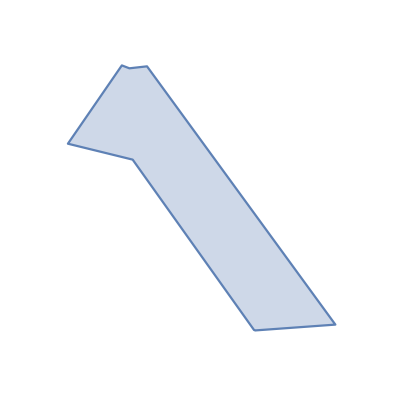

```mathematica
Module[{finalsol,points,fst,reg,cent,newpts,finalreg,plot},
finalsol=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Possible Solutions/PoSol 500G 50P.m"];
points={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},{x7,y7}}/.finalsol[[2]];
fst=FindShortestTour[points];
points=points[[fst[[2]]]];
reg=Polygon[points];
cent=RegionCentroid[reg];
newpts={#[[1]]-cent[[1]],#[[2]]-cent[[2]]}&/@points;
finalreg=Polygon[newpts];
Print[plot=RegionPlot[finalreg,PlotRange->{{-1,1},{-1,1}},Frame->False,Axes->False]];
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/Images/FinalSol Picture.jpg",plot];]
```

## Experimental Testing

## Sound Analysis and Comparison